# tmpde

## Last Updated: 05/21/2022

```mathematica
(*Quit[];*)
```

```mathematica
(*Remove["Global`*"];
ClearInOut[];*)
```

## General

## Plotting

```mathematica
(*set plot options*)
SetOptions[Plot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListLinePlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic,GridLines->Automatic];
SetOptions[ListLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];SetOptions[ListLogLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set signal plot options*)
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set 3d plot options*)
SetOptions[ListDensityPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot3D,Background->None,ImageSize->Large];
```

## Evaluations

```mathematica
(*turn upsetting things off*)
ParallelEvaluate[
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[Power::infy];
Off[FindFit::nrjnum];
Off[Infinity::indet];
];
```

## Functions

### General

```mathematica
(*play sound when finished*)
Done[type_:"email",msg_:""]:=With[{soundDJ=Play[Sin[600*π*t],{t,0,0.6}]},
Switch[type,
"text",SendMessage["SMS",msg],
"email",SendMail[<|"To"->"claytonho@g.ucla.edu","Subject"->ToString[$MachineName],"From"->"claytonho@physics.ucla.edu","Server"->"smtp.physics.ucla.edu","EncryptionProtocol"->"SSL","PortNumber"->465,"UserName"->"claytonho@physics.ucla.edu","Body"->msg,"Password"->"I2Ic1zIS2R"|>],"none",EmitSound[soundDJ]
];
];
```

### Dataset Processing

```mathematica
(*import raw counts and demodulate*)
ProcessDatasetCounts[filename_]:=Module[
{
(*actual data*)
dataset,
datasetFrequencies=Import[filename,{"/datasets/xArr"}],
datasetCounts=Import[filename,{"/datasets/results"}],
correlatedSignal,correlatedAmplitude,correlatedPhase,
(*parameters*)
modulationAmplitude=Import[filename,{"/datasets/modulation_amplitude_vpp"}],
shimVoltage=Import[filename,{"/datasets/dc_channel_voltage"}],
(*processing*)
results
},

(*refine dataset*)
dataset=AssociationThread[datasetFrequencies->datasetCounts];
(*dataset=KeySort[dataset];*)

(*demodulate counts*)
correlatedSignal=KeyValueMap[
Total[Exp[ⅈ*(2*π*#1*1*^6)*#2]]/Length[#2]&,
dataset
];
{correlatedAmplitude,correlatedSignal}=Transpose[AbsArg[correlatedSignal]];

(*format data*)
results=Transpose[
{datasetFrequencies,ConstantArray[shimVoltage,Length[correlatedAmplitude]],##}&@@{correlatedAmplitude,correlatedSignal}
];

(*clean up mess*)
Remove[dataset,datasetFrequencies,datasetCounts];
ClearSystemCache[];
ClearInOut[];

(*return dataset*)
Return[results];
]
```

```mathematica
(*import already demodulated dataset*)
ProcessDataset[filename_]:=Module[
{
(*actual data*)
datasetRaw=Import[filename,{"/datasets/results"}],
(*parameters*)
(*modulationAmplitude=Import[filename,{"/datasets/modulation_amplitude_vpp"}],
shimVoltage=Import[filename,{"/datasets/dc_channel_voltage"}],*)
(*processing*)
results
},

(*refine dataset*)
(*dataset=KeySort[dataset];*)

(*format data*)
(*results=Transpose[
(datasetRaw[[;;,1]],ConstantArray[shimVoltage,Length[datasetRaw]],datasetRaw[[;;,3]],datasetRaw[[;;,4]]}
];*)
results=datasetRaw;

(*clean up mess*)
Remove[datasetRaw];
ClearSystemCache[];
ClearInOut[];

(*return dataset*)
Return[results];
]
```

## User Input

## Parameters

```mathematica
(*top level directory for imports*)
directoryString="Z:\\motion\\Data\\2023-05-22";
(*directoryString="/Volumes/groups/motion/Data/2023-05-15";*)
(*directoryString="/Users/claytonho/Documents/Research/Science/Micromotion/RF Modulation";*)
```

```mathematica
(*select run*)
rid=21580;
```

## Process User Input

```mathematica
(*select file with give RID from all subdirectories*)
filenamesAll=FileNames["*.h5",directoryString,Infinity];
filenamesDJ=Select[filenamesAll,StringContainsQ[#,ToString[rid]]&];
```

```mathematica
(*just select dataset of interest as the first one that shows up that matches our RID*)
filenameDJ=First@filenamesDJ;
```

### Validate Input

```mathematica
(*check input directory exists*)
If[!DirectoryQ[directoryString],
MessageDialog["Failure :(\nError: Import directory not found ("<>directoryString<>")."];
FrontEndTokenExecute["EvaluatorAbort"];
];
```

```mathematica
(*check desired file exists*)
If[!FileExistsQ[filenameDJ],
MessageDialog["Failure :(\nError: Specified file not found ("<>filenameDJ<>")."];
FrontEndTokenExecute["EvaluatorAbort"]
];
```

```mathematica
(*check desired file is correct for processing*)
If[!StringContainsQ[filenamesDJ[[1]],"precool",IgnoreCase->True],
MessageDialog["Failure :(\nError: Selected file incompatible with this Notebook.\nSelected file: "<>filenameDJ<>"."];
FrontEndTokenExecute["EvaluatorAbort"]
];
```

```mathematica
(*raise message dialog to let user know everything is OK*)
(*MessageDialog["Success!\nDesired file found: "<>filenameDJ];*)
```

## Work

## Import

```mathematica
(*import and process data*)
dataset=ProcessDataset[filenameDJ];
(*sort dataset*)
dataset=SortBy[dataset,First];
```

```mathematica
(*get readout configuration*)
expArgs=Import[filenameDJ,{"Attributes","/arguments"}];
frequencyReadoutMHz=expArgs["freq_readout_mhz"];
timeReadoutus=expArgs["time_readout_us"];
```

## Process

```mathematica
countsAveraged=GroupBy[dataset,First->Last,Mean]//KeySort;
```

## Format/Plot

### Format Tables

```mathematica
(*(*format params*)
{coolingAmplitude,coolingFrequency}=Import[filenameDJ,{{"/datasets/cooling_ampl_pct","/datasets/cooling_freq_mhz"}}];
ddsFrequencykHz=dataset[[1,1]]*1000;
tableParamsSys={#}&/@{numCounts,ddsFrequencykHz,modAttenuation,coolingAmplitude,coolingFrequency};*)
```

```mathematica
(*(*create formatted data tables*)
parameterTable=TableForm[
tableParamsSys,
TableHeadings->{{"# Counts","DDS Freq. (kHz)", "DDS Att. (dB)","397nm Freq. (MHz)","397nm Ampl. (% Ampl.)"},{"System"}},
TableAlignments->{Right,Right}
];*)
```

### Plot Data

```mathematica
countPlot=ListPlot[
countsAveraged,
PlotRange->Full,
(*PlotStyle->Hue/@(voltageSignalDataset[[;;,1]]/Max[voltageSignalDataset[[;;,1]]]),*)
FrameLabel->{ 
{Style["Counts per 100 μs",{Black,Directive[15]}],None},
{Style["DDS Amplitude (%)",{Black,Directive[15]}],Style["Precooling Test - RID: "<>ToString[rid],{Black,Directive[15]}]}
}
];
```

## Summary

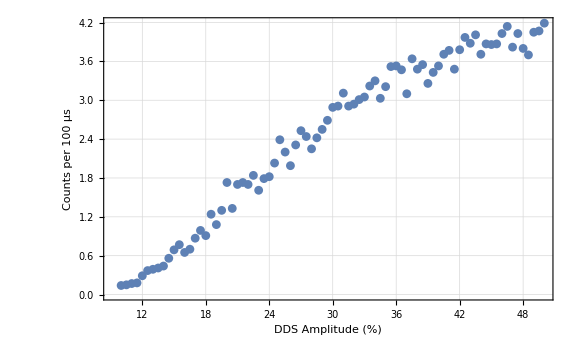

```mathematica
(*parameterTable*)
{
countPlot
}
```

```mathematica
(*tmp*)
(*res120mhz100us=Transpose[{Keys[countsAveraged],Values[countsAveraged]}];*)
(*res115mhz100us=Transpose[{Keys[countsAveraged],Values[countsAveraged]}];*)
(*res110mhz100us=Transpose[{Keys[countsAveraged],Values[countsAveraged]}];*)
(*res105mhz100us=Transpose[{Keys[countsAveraged],Values[countsAveraged]}];*)
(*res122mhz100us=Transpose[{Keys[countsAveraged],Values[countsAveraged]}];*)
res125mhz100us=Transpose[{Keys[countsAveraged],Values[countsAveraged]}];
```

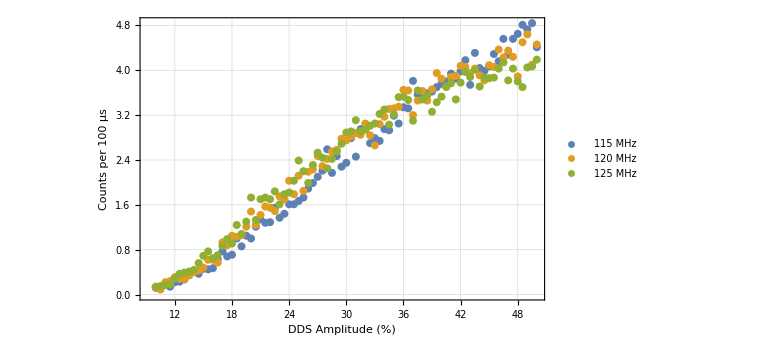

```mathematica
th0=<|105->res105mhz100us,110->res110mhz100us,115->res115mhz100us,120->res120mhz100us,122->res122mhz100us|>;
ListPlot[
{
res115mhz100us,
res120mhz100us,
res125mhz100us
},
PlotRange->Full,
PlotLegends->{"115 MHz","120 MHz","125 MHz"},
PlotStyle->{{PointSize[0.01]},{PointSize[0.01]},{PointSize[0.01]}},
FrameLabel->{ 
{Style["Counts per 100 μs",{Black,Directive[15]}],None},
{Style["DDS Amplitude (%)",{Black,Directive[15]}],Style["Precooling Test - RID: "<>ToString[rid],{Black,Directive[15]}]}
}
]
```